Using the τ non-dimensionalization of the hydrodynamic model, analytically solve for critical activity with respect to γ̇ under the assumption that k=l=0

```mathematica
Solve[(τ a)/η==((1+σ τ)^2/(γd τ)+γd τ)/((λ(1+σ τ))/(γd τ(1+γd^2 τ^2))-(γd λ τ)/(1 + γd^2 τ^2)),σ]//FullSimplify
```

{{σ→(a λ τ-2 η (1+γd^2 τ^2)-τ √(a^2 λ^2-4 γd^2 η (1+γd^2 τ^2) (η+a λ τ+γd^2 η τ^2)))/(2 η τ (1+γd^2 τ^2))},{σ→-1/τ+(a λ+√(a^2 λ^2-4 γd^2 η (1+γd^2 τ^2) (η+a λ τ+γd^2 η τ^2)))/(2 (η+γd^2 η τ^2))}}

```mathematica
Subscript[σ, 1]=(-2 η τ+a λ τ^2-2 γd^2 η τ^3-τ^2 √(-4 γd^2 η^2+a^2 λ^2-4 a γd^2 η λ τ-8 γd^4 η^2 τ^2-4 a γd^4 η λ τ^3-4 γd^6 η^2 τ^4))/(2 (η τ^2+γd^2 η τ^4))/.{η->1,τ->1,λ->1};
Subscript[σ, 2]=(-2 η τ+a λ τ^2-2 γd^2 η τ^3+τ^2 √(-4 γd^2 η^2+a^2 λ^2-4 a γd^2 η λ τ-8 γd^4 η^2 τ^2-4 a γd^4 η λ τ^3-4 γd^6 η^2 τ^4))/(2 (η τ^2+γd^2 η τ^4))/.{η->1,τ->1,λ->1};
```

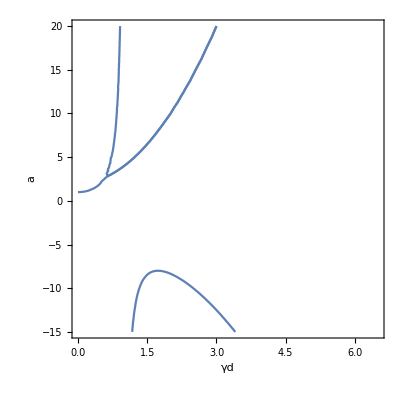

```mathematica
p1=ContourPlot[Re[Subscript[σ, 1]]==0,{γd,0,6.5}, {a,-15,20},AxesLabel->Automatic];
p2=ContourPlot[Re[Subscript[σ, 2]]==0,{γd,0,6.5}, {a,-15,20},AxesLabel->Automatic];
Show[p1,p2]
```

```mathematica
There is a clear qualitative and quantitative difference between this analytic result and the computational result...1) Asymptote at γd=1 for both branches 2) the critical activity for γd =0 is 1 instead of ~0.6 as seen in computational studies.
```

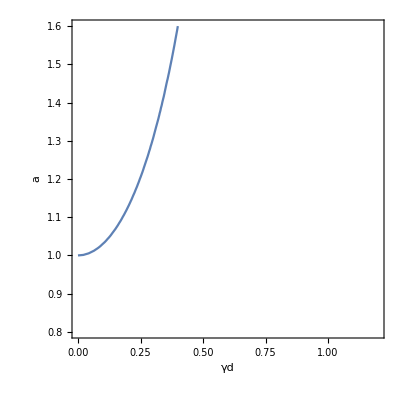

```mathematica
ContourPlot[Subscript[σ, 2]==0,{γd,0,1.2}, {a,0.8,1.6},AxesLabel->Automatic]
```

```mathematica
Subscript[σ, 1]
```

1/2 Re[1/(1+γd^2)(-2+a-2 γd^2-√(a^2-4 γd^2-4 a γd^2-8 γd^4-4 a γd^4-4 γd^6))]

```mathematica
Subscript[σ, 2]
```

(-2+a-2 γd^2+√(a^2-4 γd^2-4 a γd^2-8 γd^4-4 a γd^4-4 γd^6))/(2 (1+γd^2))

```mathematica
fig =-Graphics-;
```

```mathematica
data = Cases[fig//Normal, Line[a_]:>a,Infinity];
Export["analytic-data.dat",data]
```

analytic-data.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["analytic-data.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["analytic-data.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["analytic-data.txt"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["analytic-data.dat"]]]
```

```mathematica
sigsoln = Solve[(τ a)/η==((1+ ⅈ σ τ)^2/(γd τ)+γd τ)/((λ(1+ⅈ σ τ))/(γd τ(1+γd^2 τ^2))-(γd λ τ)/(1 + γd^2 τ^2)),σ]//FullSimplify
```

{{σ→(ⅈ (-a λ τ^2+2 η (τ+γd^2 τ^3)+ⅈ √(τ^4 (-a^2 λ^2+4 γd^2 η (1+γd^2 τ^2) (η+a λ τ+γd^2 η τ^2)))))/(2 τ^2 (η+γd^2 η τ^2))},{σ→(-ⅈ a λ τ^2+2 ⅈ η (τ+γd^2 τ^3)+√(τ^4 (-a^2 λ^2+4 γd^2 η (1+γd^2 τ^2) (η+a λ τ+γd^2 η τ^2))))/(2 τ^2 (η+γd^2 η τ^2))}}

```mathematica
σ/.sigsoln[[1,1]] /. τ->1 /. η->1/.λ->1
```

(ⅈ (-a+2 (1+γd^2)+ⅈ √(-a^2+4 γd^2 (1+γd^2) (1+a+γd^2))))/(2 (1+γd^2))

```mathematica
((γd^2+(1+ⅈ y)^2)(1+γd^2)(1-γd^2-ⅈ y))/((1-γd^2)^2+y^2)//Expand
```

1/(y^2+(1-γd^2)^2)+(ⅈ y)/(y^2+(1-γd^2)^2)+y^2/(y^2+(1-γd^2)^2)+(ⅈ y^3)/(y^2+(1-γd^2)^2)+γd^2/(y^2+(1-γd^2)^2)-(2 ⅈ y γd^2)/(y^2+(1-γd^2)^2)+(2 y^2 γd^2)/(y^2+(1-γd^2)^2)+(ⅈ y^3 γd^2)/(y^2+(1-γd^2)^2)-γd^4/(y^2+(1-γd^2)^2)-(3 ⅈ y γd^4)/(y^2+(1-γd^2)^2)+(y^2 γd^4)/(y^2+(1-γd^2)^2)-γd^6/(y^2+(1-γd^2)^2)

```mathematica
1/(y^2+(1-γd^2)^2)+y^2/(y^2+(1-γd^2)^2)+γd^2/(y^2+(1-γd^2)^2)+(2 y^2 γd^2)/(y^2+(1-γd^2)^2)-γd^4/(y^2+(1-γd^2)^2)+(y^2 γd^4)/(y^2+(1-γd^2)^2)-γd^6/(y^2+(1-γd^2)^2)//FullSimplify
```

((1+y^2-γd^2) (1+γd^2)^2)/(y^2+(-1+γd^2)^2)

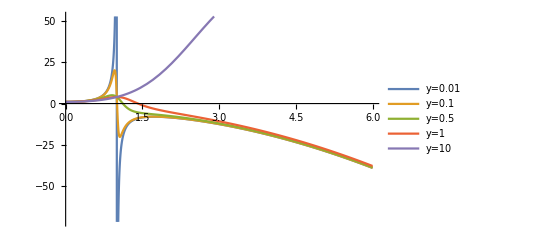

{(1-γd^4+(1+γd^2)^3)/(1.0001+γd^2),(1-γd^4+(1+γd^2)^3)/(1.01+γd^2),(1-γd^4+(1+γd^2)^3)/(1.25+γd^2),(1-γd^4+(1+γd^2)^3)/(2+γd^2),(1-γd^4+(1+γd^2)^3)/(101+γd^2)}

```mathematica
(* Oscillatory Degrees of Freedom ?? *)
f[γd_]=((1+y^2-γd^2) (1+γd^2)^2)/(y^2+(-1+γd^2)^2);
Y = {0.01,0.1,0.5,1,10};
Plot[{f[γd]/.y->0.01,f[γd]/.y->0.1,f[γd]/.y->0.5,f[γd]/.y->1,f[γd]/.y->10},{γd,0,6},PlotLegends->{"y=0.01","y=0.1","y=0.5","y=1","y=10"}]
```

```mathematica
sigmasoln = Solve[(τ a)/η==((1+σ τ)^2/(γd τ)+γd τ)/((λ(1+σ τ))/(γd τ(1+γd^2 τ^2))-(γd λ τ)/(1 + γd^2 τ^2)),σ]/.{τ->1,η->1,λ->1}//FullSimplify
```

```mathematica
sigmasoln={{σ1->-1/(2 (1+γd^2))(2-a+2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))},{σ2->1/(2 (1+γd^2))(-2+a-2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))}};
```

```mathematica
(σ1/.sigmasoln[[1]] ) +(σ2/.sigmasoln[[2]])
```

(-2+a-2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))/(2 (1+γd^2))-(2-a+2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))/(2 (1+γd^2))

```mathematica
-(2-a+2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))/(2 (1+γd^2))+σ2
```

-(2-a+2 γd^2+√(a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4)))/(2 (1+γd^2))+σ2

This Following Section Shows that the real part of σ is exactly that which is not under the square root!

```mathematica
aval = 2;
(*RealSig[γd_] = Re[σ/.sigmasoln[[1]]]/.a->aval;
NonSqrtPart[γd_]=-(2-a+2 γd^2)/(2 (1+γd^2));*)
SqrtPart[γd_]=a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4);
NSolve[SqrtPart[γd]==0/.a->aval];
(*Plot[ {Re[σ/.sigmasoln[[1]]]/.a->aval,NonSqrtPart[γd]/.a->aval,Im[σ/.sigmasoln[[1]]]/.a->aval},{γd,0,2},PlotLegends->{"Re[σ]","Non-Square-Root[σ]","Im[σ]"}];
Plot[ {Re[σ/.sigmasoln[[2]]]/.a->aval,NonSqrtPart[γd]/.a->aval,Im[σ/.sigmasoln[[2]]]/.a->aval},{γd,0,2},PlotLegends->{"Re[σ]","Non-Square-Root[σ]","Im[σ]"}];*)
```

-Graphics-

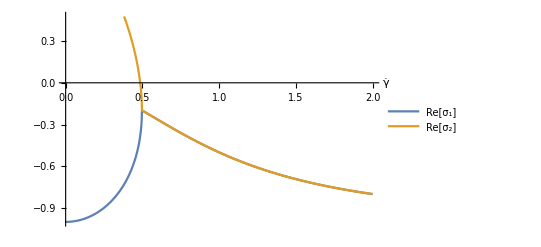

```mathematica
Plot[ {Re[σ1/.sigmasoln[[1]]]/.a->aval,Re[σ2/.sigmasoln[[2]]]/.a->aval},{γd,0,2},PlotLegends->{"Re[σ_1]","Re[σ_2]"},AxesLabel->{OverDot[γ]}]
```

```mathematica
{Re[σ1/.sigmasoln[[1]]]/.a->aval,Re[σ2/.sigmasoln[[2]]]/.a->aval}
```

{-1/2 Re[(2 γd^2+√(4-4 (γd+γd^3)^2-8 (γd^2+γd^4)))/(1+γd^2)],1/2 Re[(-2 γd^2+√(4-4 (γd+γd^3)^2-8 (γd^2+γd^4)))/(1+γd^2)]}

{17.,{γd→1.}}

22.

```mathematica
aval = 6;
SqrtPart[γd_] = a^2-4 (γd+γd^3)^2-4 a (γd^2+γd^4);
NSolve[SqrtPart[γd]==0/.a->aval,γd]
NSolve[NonSqrtPart[γd]==0/.a->aval,γd]
```

{{γd→-0.831672},{γd→0.-1.3864 ⅈ},{γd→0.+1.3864 ⅈ},{γd→0.-2.60184 ⅈ},{γd→0.+2.60184 ⅈ},{γd→0.831672}}

{{γd→-1.41421},{γd→1.41421}}

```mathematica
{{γd->-0.9316611999652723},{γd->0.-1.4502012635712025 ⅈ},{γd->0.+1.4502012635712025 ⅈ},{γd->0.-2.9605588807955194 ⅈ},{γd->0.+2.9605588807955194 ⅈ},{γd->0.9316611999652724}}
```

{{γd→-0.931661},{γd→0.-1.4502 ⅈ},{γd→0.+1.4502 ⅈ},{γd→0.-2.96056 ⅈ},{γd→0.+2.96056 ⅈ},{γd→0.931661}}

```mathematica
σ/.sigmasoln[[1]]/.{a->3,γd->0.611787}
```

0.091478-0.00178392 ⅈ